```mathematica
Clear["Global`*"]

(*Relevant gain pp.*)


rG[x_]:=Exp[-α*x^β]/biggestgain;
G[x_]:=Exp[-α*x^β];
Gmeas[t_]=λ*Pi*InverseFunction[G][t]^2;
Gmeasr[t_,biggestgain_]=λ*Pi*InverseFunction[G][t*biggestgain]^2;

avoidance[t_]:=Exp[-Gmeas[t]];(*Avoidance function.*)
(*NπN pdf*)
(*Ehdolla  G(\|x\|) pienempi kuin r, mikä on jakauma*)

avoidance[t]

-Gmeas'[t]
Gmeasr[t,u]

(2 ⅇ^(-π (-Log[t])^(2/b)) π (-Log[t])^(-1+2/b))/(b t)

 (*t<biggestgain*)
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

ⅇ^(-π λ (-Log[t]/α)^(2/β))

(2 π λ (-Log[t]/α)^(-1+2/β))/(t α β)

π λ (-Log[t u]/α)^(2/β)

(2 ⅇ^(-π (-Log[t])^(2/b)) π (-Log[t])^(-1+2/b))/(b t)

```mathematica
Integrate[(1-1/(1+s*t))*(2 π λ (-Log[t]/α)^(-1+2/β))/(t α β),{t,0,1}]
```

```mathematica
β=2;
Exp[(2 π (1/α)^(2/β) λ Gamma[2/β] PolyLog[2/β,-s])/β]
```

(1+s)^(-(π λ)/α)

```mathematica
Clear["Global`*"]
Integrate[(2 ⅇ^(-π λ (-Log[t]/α)^(2/β)) π λ (-Log[t]/α)^(-1+2/β))/(t α β)*(1+θ/t)^(-(π λ)/α),{t,0,1}]
```

$Aborted

```mathematica
FullSimplify[1/2 (θ/(1+θ))^(-(π λ)/α) Hypergeometric2F1[(π λ)/α,(2 π λ)/α,1+(2 π λ)/α,-1/(θ/(1+θ))],Assumptions->{θ>0,a>0}]
```

1/2 (θ/(1+θ))^(-(π λ)/α) Hypergeometric2F1[(π λ)/α,(2 π λ)/α,1+(2 π λ)/α,-(1+θ)/θ]

```mathematica
(*Gamma approximation*)
Clear["Global`*"]

Integrate[(2 ⅇ^(-π λ (u/α)^(2/β)) π λ (u/α)^(-1+2/β))/(α β)*Exp[-u],{u,0,Infinity}]
```

∫_0^∞ (2 ⅇ^(-u-π (u/α)^(2/β) λ) π (u/α)^(-1+2/β) λ)/(α β)ⅆu

```mathematica
f[s_]:=Exp[(2 π (1/α)^(2/β) λ Gamma[2/β] PolyLog[2/β,-s])/β];
```

General::munfl: Exp[-1203.83] is too small to represent as a normalized machine number; precision may be lost.

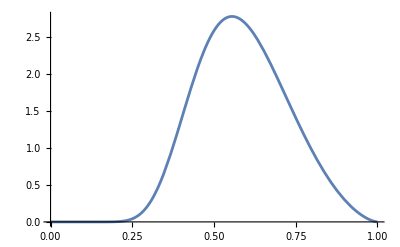

```mathematica
β=0.8;
Plot[(2 ⅇ^(-π λ (-Log[t]/α)^(2/β)) π λ (-Log[t]/α)^(-1+2/β))/(t α β),{t,0,1}]
```